```mathematica
f[x_]:=x^2
```

```mathematica
table=Table[{x,f[x]},{x,-1.75,1.75,0.2}]
```

{{-1.75,3.0625},{-1.55,2.4025},{-1.35,1.8225},{-1.15,1.3225},{-0.95,0.9025},{-0.75,0.5625},{-0.55,0.3025},{-0.35,0.1225},{-0.15,0.0225},{0.05,0.0025},{0.25,0.0625},{0.45,0.2025},{0.65,0.4225},{0.85,0.7225},{1.05,1.1025},{1.25,1.5625},{1.45,2.1025},{1.65,2.7225}}

```mathematica
theXs=Transpose[table][[1]];
theFs=Transpose[table][[2]];
```

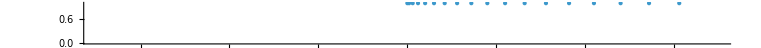

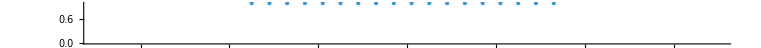

```mathematica
NumberLinePlot[theFs,PlotRange->{-3.5,3.5}]
NumberLinePlot[theXs,PlotRange->{-3.5,3.5}]
```